```mathematica
θ''[t]+g/l Sin[θ[t]] ==0
```

(g Sin[θ[t]])/l+θ''[t]==0

```mathematica
T = 4(l/g)^(1/2)Integrate[1/(1-Sin[θ/2]^2 Sin[p]^2)^(1/2),{p,0,Pi/2}]
```

(4 √(l/g) EllipticK[-Tan[θ/2]^2])/(√(Cos[θ/2]^2))

```mathematica
(4 √(l/g) Series[EllipticK[-Tan[θ/2]^2],{θ,0,6}])/(√(Cos[θ/2]^2))
```

2 √(l/g) π+1/8 √(l/g) π θ^2+(11 √(l/g) π θ^4)/1536+(173 √(l/g) π θ^6)/368640+O[θ]^7

```mathematica
g:=9.81
```

```mathematica
l:=1
```

```mathematica
NDSolve[{θ''[t]+g/l Sin[θ[t]] ==0,θ[0]== Pi/2,θ'[0]==0,WhenEvent[θ[t]==0,Print[t]]},θ,{t,0,10}]
```

0.591961

1.77588

2.9598

4.14372

5.32764

6.51157

7.69549

8.87941

{{θ→InterpolatingFunction[…]}}

```mathematica
θ = Pi/2
```

π/2

```mathematica
N[2 √(l/g) π+1/8 √(l/g) π θ^2+(11 √(l/g) π θ^4)/1536+(173 √(l/g) π θ^6)/368640,15]
```

2.36623

```mathematica
2.959802378469718-0.5919605020120086
```

2.36784

```mathematica
NDSolve[{θ''[t]+g/l Sin[θ[t]] ==0,θ[0]== Pi/2,θ'[0]==0,WhenEvent[θ[t]==0,Print[t]]},θ,{t,0,10},Method->ExplicitEuler,StartingStepSize->0.0562288]
```

0.607687

1.98511

8.98002

{{θ→InterpolatingFunction[…]}}

```mathematica
8.980021693459301-0.6076867426182945
```

8.37233

```mathematica
solc :=NDSolve[{x'[t]==y[t],y'[t]==-g/l Sin[x[t]],x[0]== Pi/2,y[0]==0},{x[t],y[t]},{t,0,10}]
```

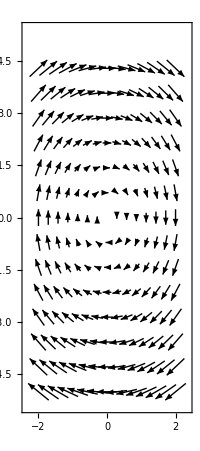

```mathematica
vfield := VectorPlot[{v, -2*x}, {x, -2,2}, {v,-5,5}, PlotTheme->"Monochrome",AspectRatio->Automatic]
vfield
```

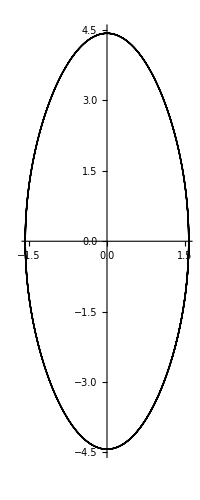

```mathematica
solline := ParametricPlot[Evaluate[{x[t], y[t]} /. solc], {t, 0, 10}, PlotTheme->"Monochrome", PlotStyle->Thick]
solline
```

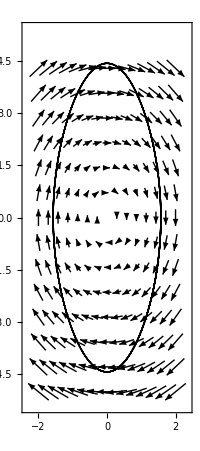

```mathematica
Show[{vfield, solline}]
```

```mathematica
θinit :=Pi/2
ω0:=(g/l)^(1/2)
ω:=(ω0^2/(1+(θinit^2)/8))^(1/2)
```

```mathematica
θanal[t_]:=θinit*Cos[ω*t]+((θinit^3)(Cos[3ω*t]-Cos[ω*t]))/192
```

```mathematica
theta :=NDSolve[{θ''[t]+g/l Sin[θ[t]] ==0,θ[0]== Pi/2,θ'[0]==0},θ,{t,0,10}]
```

```mathematica
Plot[{{θanal[t]},Evaluate[θ[t] /. theta]}, {t, 0, 10},PlotLegends->"Expressions",AspectRatio->Automatic]
```